# Import from FORM

## How does import time depend on output size and structure?

This notebook generates its own fixtures. Export and FORM execution are preparation steps, outside import timing. Repeated imports use the same saved files. Full includes the complete bubble.

## 1. Setup

Use a fresh kernel for reproducible measurements. Mathematica, FeynGrav with FeynCalc, and FORM/TFORM are sufficient. No Python, shell scripts or external fixtures are needed. Opening this notebook does not execute any cells.

```mathematica
setupSeconds=First[AbsoluteTiming[Get[FileNameJoin[{NotebookDirectory[],"Support","Benchmark.wl"}]];]];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynGrav 4.0

FeynGrav: Use FeynGravCommands to print the list of all commands.

FeynGrav: On initialization, the package only imports libraries for matter with spin s = 0, 1/2, 1, and 2 with minimal couplings up to the second order. To import additional libraries, use the "import*" command.

FeynGrav: Core publications on FeynGrav are [Class.Quant.Grav. 39 (2022) 16, 165006](https://doi.org/10.1088/1361-6382/ac7e15), [Comput.Phys.Commun. 292 (2023) 108871](https://doi.org/10.1016/j.cpc.2023.108871), [Comput.Phys.Commun. 310 (2025) 109508](https://doi.org/10.1016/j.cpc.2025.109508), [arXiv:2510.17320](https://doi.org/10.48550/arXiv.2510.17320)

## 2. Choose a profile

Replace None below with "Quick" or "Full". Until you do, evaluation skips the benchmarks. Quick uses three measured small trials and one measured substantial trial; Full uses five and three, respectively. One warmup is recorded separately. Full workloads can take substantial time and disk space.

```mathematica
config=BenchmarkConfiguration[];
config["Profile"]="Full";
config["FORMExecutable"]=Automatic;
config["TFORMExecutable"]=Automatic;
config["Workers"]=Automatic;
config["Repetitions"]=Automatic;
config["PhysicalRepetitions"]=Automatic;
config["ExecutionTimeout"]=Automatic;
config["OutputDirectory"]=Automatic;
cleanupSuccessfulFiles=False;
```

Automatic uses PATH discovery, profile trial counts, and a unique directory under the system temporary directory. Supply absolute executable paths if your desktop kernel has a different PATH. Timeouts are 60 seconds per FORM execution in Quick and 600 in Full; they do not bound export, import or the entire notebook. Worker defaults are capped at the reported processor count; you may explicitly choose other counts.

## 3. Prepare inputs and check the environment

```mathematica
prepared=BenchmarkPrepare["Import",config];
If[AssociationQ[prepared],prepared["SetupSeconds"]=setupSeconds;];
```

Checking FORM

Preparing inputs; this is outside export, execution and import measurements.

Prepared metric-trace

Prepared free-indices

Prepared supported-scalars

Prepared repeated-products-100

Prepared repeated-products-1000

Prepared repeated-products-5000

Prepared distinct-products-100

Prepared distinct-products-1000

Prepared distinct-products-5000

Prepared full-bubble

```mathematica
If[AssociationQ[prepared],Dataset[KeyTake[prepared,{"Environment","Checks","Configuration","SetupSeconds"}]]]
```

Preparation constructs inputs and loads any required libraries. Import fixtures are generated at the start of each case in the following cell, before import measurements. Missing executables are recorded and dependent cases are skipped. No installation is attempted.

## 4. Run sequential measurements

For a new run, evaluate the preparation cell again first. Each prepared run can be executed once; previous reports are preserved.

```mathematica
report=BenchmarkRun[prepared];
```

Benchmark: metric-trace

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: free-indices

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: supported-scalars

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: repeated-products-100

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: repeated-products-1000

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: repeated-products-5000

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: distinct-products-100

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: distinct-products-1000

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: distinct-products-5000

Preparing FORM output before import trials.

Preparation 0: export

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Measured 4: import (1 worker configuration)

Measured 5: import (1 worker configuration)

Benchmark: full-bubble

Preparing FORM output before import trials.

Preparation 0: export

FORM Execute: 10.01 s elapsed (wall clock).

FORM Execute: 20.02 s elapsed (wall clock).

FORM Execute: 30.04 s elapsed (wall clock).

FORM Execute: 40.04 s elapsed (wall clock).

FORM Execute: 50.06 s elapsed (wall clock).

FORM Execute: 60.06 s elapsed (wall clock).

Warmup 0: import (1 worker configuration)

Measured 1: import (1 worker configuration)

Measured 2: import (1 worker configuration)

Measured 3: import (1 worker configuration)

Reports: /tmp/cfc-benchmark-7b3ff9e0-13da-4c5a-9295-dd84dfdb63e9/report.json

## 5. Inspect results and validation

```mathematica
BenchmarkSummary[report]
```

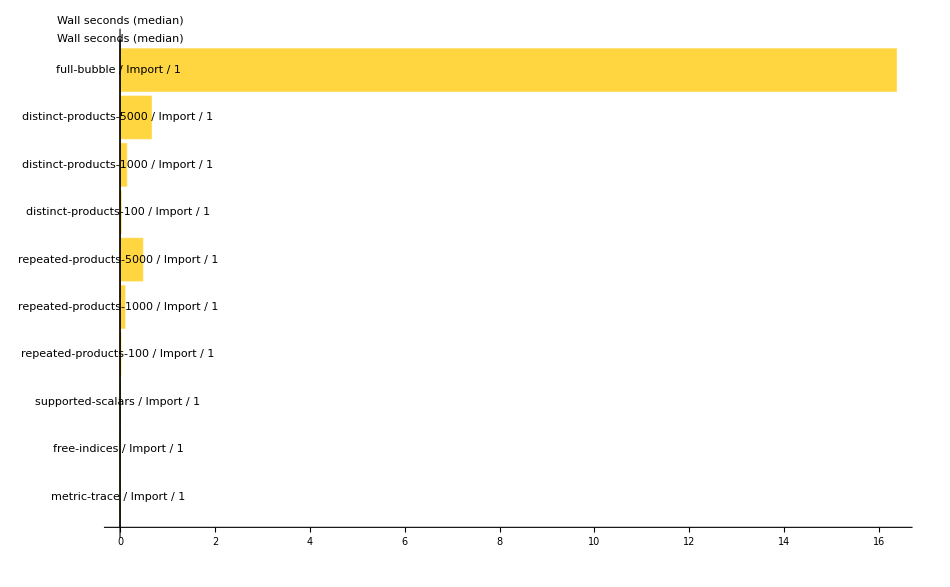

```mathematica
BenchmarkPlot[report]
```

```mathematica
If[AssociationQ[report],Dataset[(KeyTake[#1,{"Case","Stage","Workers","Phase","Trial","Seconds","Status","Validation","ValidationMethod","FirstBenchmarkImportInKernel"}]&)/@report["Rows"]]]
```

Only successful, verified measured trials enter the timing summary. A single trial is one observation, not a variability estimate. Known small answers are checked algebraically; larger cases are checked for repeatability and agreement across execution paths, not against an independent physics calculation. Baseline means that a comparison result has been recorded but has not yet been matched. Inconclusive and timed-out comparisons are excluded.

## 6. Interpret and retain the report

All timings are wall-clock seconds. First-import and warmup observations remain separate from measured repetitions. A first benchmark import is not necessarily a cold kernel import if you previously used the converter. Setup, validation, fingerprinting and display are outside stage timers. StageSum adds export, execution and import times; Calculate measures the separate public call including its availability check. Initialization, filesystem caches, background load and temperature can affect timings. These observations do not guarantee a speedup on another machine.

```mathematica
If[AssociationQ[report],report["Directory"]]
```

/tmp/cfc-benchmark-7b3ff9e0-13da-4c5a-9295-dd84dfdb63e9

The run directory contains report.json, summary.csv and working files. Reports include source hashes and raw observations. The system may remove temporary files later; choose a persistent OutputDirectory before a run if you want to keep results. Cleanup is optional, deletes only successful owned working directories, and retains reports and failure logs.

```mathematica
If[TrueQ[cleanupSuccessfulFiles]&&AssociationQ[report],BenchmarkCleanup[report]]
```